```mathematica
(*This Mathematica notebook uses GUTCP to calculate how long the universe has been expanding (in the current cycle) and what the cosmic microwave background temperature was at the start of the expansion. The answers are 120 billion years ago at a temperature of 4.5 Kelvin. It also calculates the mass at maximum expansion is about 90% of the mass at the start.  These numbers differ from those reported in the book.  
Your comments and criticisms are solicited.

Caveat:  Randell Mills has specifically denied me "permission to use my copyrighted equations and theory in an algebraic manipulation to invert them to fundamental constants which are the input parameters.  The same could be done with all observables and my exact equations." 

Charitable interpretations of his denial:

1) An error on my part could result in material damage to his business.  Having granted him this charitable interpretation, I'll assert that the following may very well be in error in some potentially damaging way which is why I'd like now to ask for help in identifying the error in the following derivation.
 2)Even if the following derivation is basically correct, it may be misconstrued as attributing to me, rather than Randell Mills and colleagues, a major Advance in cosmology.  The derivation, if correct, is a trivial result of the non-trivial GUTCP.  The fact that I may have published the result first shouldn't be taken to assign credit to me for this advance.  After all, Mills and colleagues have their hands full fighting battles so there are bound to be corrections in the details of the previously published books and/or papers involving GUTCP.    Consider this work, even if correct, little more than proof-reading.
 
With that caveat said, let me explain what I did:  

The JWST observations motivated me to look into using GUTCP's formulas to derive a theoretic value of H0 (which we can call H0GUTCP) from physical constants (c, G, sigma and e(missivity of blackbody)) and the observed cosmic microwave background radiation temperature.  It turns out there is a solution for the Hubble constant within GUTCP using only Newton's gravitational constant and the microwave background temperature as parameters with any uncertainty. Other physical constants have been relegated to zero uncertainty by the 2019 CODATA. This avoids relying on the estimated mass of the universe (mU) provided by observational extrapolations independently of the CMBR Temperature. 
The formula for H0GUTCP can be derived by first solving for mU* in terms of CMBR Temperature and then using that to solve for H as a function of time, then substituting the time since start of the last expansion to get H0. 

The relevant formulas are:

1)The aleph (radius of the universe) equation under "The Expanding Universe and the Microwave Background" section.
2)The aleph_min equation (32.146)
3)Setting t=0 for aleph so that expression can be set == aleph_min to solve for mU
4)Substitute the solution for mU into (32.156) to obtain H as a function of time.
5)In H substitute tNow as obtained below for t to obtain H0.

* mU, when it appears in calculations as a constant (as opposed to a function of time) designates the maximum mass of the universe as it occurs at the minimum diameter of the universe which occurs at t=0.

HOWEVER, when I ran the H0GUTCP calculation using the tNow that Mills assumed, the H0GUTCP that I came up with was less than a factor of 2 that of the lowest currently redshift-measured estimate of H0.

This made me suspect that either the CMBR Temperature AT THE START OF THE CURRENT EXPANSION or the time since the start of the expansion or BOTH parameters needed adjustment.  That is what motivated me to write the following Mathematica script which purports to solve for BOTH parameters (tNow, CMBRTempAtStart) in terms of physical constants and direct measurements.

As for the proportion of all mass converted to energy at the end of the expansion phase (See mURadiatedAsEnergy = 12.5%):
    
Motivated by a paper on something called the S8 tension being increased by a large scale simulation of cosmological evolution, I decided to inquire into whether a change in the dark matter to light matter ratio would matter,since the standard cosmological model denies such a change in ratio-- but hydrino evolution would not.  However,the more I thought about it the more I began to wonder about something I saw in GUTCP's cosmology section stating that _all_ mass is converted into energy at the end of the expansion phase. I couldn't figure out what mechanism converted all baryonic matter to energy since it would require anti-baryons to be created, which is not discussed in GUTCP.
Note,this claim of "all" matter being converted to energy is not an aspect of the fundamental equations of GUTCP's cosmology but is rather the consequence of an equation for mU(t)-- the mass of the universe with respect to time-- that is not derived from those equations AFAIK.This reminded me of the inconsistency between commentary text and the core cosmological equations that led me to write a Mathematica notebook which solved for age of the universe at present in terms of the core equations,and came up with something like 90 billion years-- which is just under 20% of the expansion phase.So I went back to my Mathematica notebook (which Wolfram has mercilessly deleted from the web but which I saved on my computer) and derived my own mU(t) from the core cosmological equations.This function produced a mass at the end of expansion that is about 90% of the mass at the start of the expansion (the time of maximum mass and minimum radiation and minimum spacetime).This is more what I would expect of known mass to energy conversion mechanisms (including those I see in GUTCP).

The calculation says we're about 120 billion years into the present expansion and the CMBR Temperature at the start of the expansion was 4.5Kelvins.
*)
```

```mathematica
#Quit[]
aleph[t_]=(2 G mUAtStart)/c^2 + (c mUAtStart /(c^3/(4 Pi G))) - (c mUAtStart /(c^3/(4 Pi G)))*Cos[2 Pi t/(2 Pi G mUAtStart/c^3)] 
PU[t_]= c^5*(1+Cos[2 Pi t/(2 Pi G mUAtStart/c^3)])/(8 G Pi)
mURadiatedAsEnergy[t_]=Integrate[PU[t],t]/c^2
AU[t_]= 4 Pi aleph[t]^2
RU[t_]=PU[t]/AU[t]
TU[t_]=(RU[t]/(e sigma))^(1/4)
alephMin = Sqrt[c^5/((4 Pi)^2*G e sigma *CMBRTempAtStart^4)]
alephAtStart=aleph[0]
mUAtStart = First[mUAtStart/.Solve[alephMin== alephAtStart, mUAtStart] ]
mU[t_]=mUAtStart-mURadiatedAsEnergy[t] (* jabowery's mU derived from the core GUTCP cosmological equations above *)
mUBook[t_]=(mUAtStart/2 )(1+Cos[2 Pi t/(2 Pi G mUAtStart/(c^3))]) (* 32.158 *)
```

#Quit[]

(2 G mUAtStart)/c^2+(4 G mUAtStart π)/c^2-(4 G mUAtStart π Cos[(c^3 t)/(G mUAtStart)])/c^2

(c^5 (1+Cos[(c^3 t)/(G mUAtStart)]))/(8 G π)

(c^3 (t+(G mUAtStart Sin[(c^3 t)/(G mUAtStart)])/c^3))/(8 G π)

4 π ((2 G mUAtStart)/c^2+(4 G mUAtStart π)/c^2-(4 G mUAtStart π Cos[(c^3 t)/(G mUAtStart)])/c^2)^2

(c^5 (1+Cos[(c^3 t)/(G mUAtStart)]))/(32 G π^2 ((2 G mUAtStart)/c^2+(4 G mUAtStart π)/c^2-(4 G mUAtStart π Cos[(c^3 t)/(G mUAtStart)])/c^2)^2)

(((c^5 (1+Cos[(c^3 t)/(G mUAtStart)]))/(e G sigma ((2 G mUAtStart)/c^2+(4 G mUAtStart π)/c^2-(4 G mUAtStart π Cos[(c^3 t)/(G mUAtStart)])/c^2)^2))^(1/4))/(2 2^(1/4) √π)

(√(c^5/(CMBRTempAtStart^4 e G sigma)))/(4 π)

(2 G mUAtStart)/c^2

(c^2 √(c^5/(CMBRTempAtStart^4 e G sigma)))/(8 G π)

(c^2 √(c^5/(CMBRTempAtStart^4 e G sigma)))/(8 G π)-(c^3 (t+(√(c^5/(CMBRTempAtStart^4 e G sigma)) Sin[(8 c π t)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))])/(8 c π)))/(8 G π)

(c^2 √(c^5/(CMBRTempAtStart^4 e G sigma)) (1+Cos[(8 c π t)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))]))/(16 G π)

```mathematica
(*uncG = UnitConvert[Around @@ 
 Entity["PhysicalConstant", "GravitationalConstant"][{"Value", 
   "StandardUncertainty"}]]*)

uncG = QuantityMagnitude[UnitConvert[ Entity["PhysicalConstant", "GravitationalConstant"]["Value"]]]
 
(*uncCMBRTempNow = Around @@ 
 Entity["PhysicalConstant", 
   "CosmicMicrowaveBackgroundTemperature"][{"Value", 
   "StandardUncertainty"}]+Quantity[1.8,"KelvinsDifference"]*)
 
 uncCMBRTempNow  =QuantityMagnitude[UnitConvert[ Entity["PhysicalConstant",  "CosmicMicrowaveBackgroundTemperature"]["Value"]]]
```

6.674×10^-11

2.73

```mathematica
alephRate[t_]=4 Pi c Sin[2 Pi t/(2 Pi G mUAtStart/c^3)]
```

4 c π Sin[(8 c π t)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))]

```mathematica
(*H= alephRate[UnitConvert[Quantity[10^10, "Year"]]]*)
H[t_]= alephRate[t]/(c t)
LightRadius[t_]=c/H[t]
```

(4 π Sin[(8 c π t)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))])/t

(c t Csc[(8 c π t)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))])/(4 π)

```mathematica
H0GUTCP = H[tNow]
```

(4 π Sin[(8 c π tNow)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))])/tNow

```mathematica
TUNowGUTCP = TU[tNow]
```

(((c^5 (1+Cos[(8 c π tNow)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))]))/(e G sigma (1/2 √(c^5/(CMBRTempAtStart^4 e G sigma))+(√(c^5/(CMBRTempAtStart^4 e G sigma)))/(4 π)-1/2 √(c^5/(CMBRTempAtStart^4 e G sigma)) Cos[(8 c π tNow)/(√(c^5/(CMBRTempAtStart^4 e G sigma)))])^2))^(1/4))/(2 2^(1/4) √π)

```mathematica
quantitiesSubs={
e -> 1,
sigma -> QuantityMagnitude[UnitConvert[Quantity[, "StefanBoltzmannConstant"]]],
c ->QuantityMagnitude[ UnitConvert[Quantity[, "SpeedOfLight"]]],
G->QuantityMagnitude[UnitConvert[uncG]]
}
```

{e→1,sigma→(5454781984210512994952000000 π^5)/29438455734650141042413712126365436049,c→299792458,G→6.674×10^-11}

```mathematica
eqlist={
(H0GUTCP/.quantitiesSubs)== QuantityMagnitude[UnitConvert[Quantity[, "HubbleParameter"]]],
(TUNowGUTCP/.quantitiesSubs)==uncCMBRTempNow
}
```

{(4 π Sin[(9.419×10^-21 tNow)/(√(1/CMBRTempAtStart^4))])/tNow==2.×10^-18,2.122×10^14 ((1+Cos[(9.419×10^-21 tNow)/(√(1/CMBRTempAtStart^4))])/((4.636×10^29 √(1/CMBRTempAtStart^4)-4.×10^29 √(1/CMBRTempAtStart^4) Cos[(9.419×10^-21 tNow)/(√(1/CMBRTempAtStart^4))])^2))^(1/4)==2.73}

```mathematica
tNowCMBRTempAtStartListSubs=FindRoot[eqlist,{{tNow,2.6*10^18},{CMBRTempAtStart,4.15}},MaxIterations->100000]
(*(t/.FindRoot[H1,{t,356.25*3600*24*10^10}])/(356.25*3600*24)*)
```

{tNow→3.76709×10^18,CMBRTempAtStart→4.496}

```mathematica
CMBRTempAtStart = CMBRTempAtStart/.tNowCMBRTempAtStartListSubs
tNow = tNow/.tNowCMBRTempAtStartListSubs
```

4.496

3.76709×10^18

```mathematica
UnitConvert[Quantity[tNow,"Seconds"],"Years"]
```

1.19454×10^11 yr

```mathematica
(* Mass of the universe at the start of an expansion phase. *)
mUAtStart/.quantitiesSubs
```

2.12025×10^54

```mathematica
(H0GUTCP/. quantitiesSubs)*3.09*10^19
```

67.7548

```mathematica
QuantityMagnitude[UnitConvert[Quantity[, "HubbleParameter"]]]*3.09*10^19
```

67.7548

```mathematica
UnitConvert[Quantity[alephAtStart/.quantitiesSubs,"Meters"],"LightYears"]
```

3.32856×10^11 ly

```mathematica
UnitConvert[Quantity[2G mUAtStart/c^2/.quantitiesSubs,"Meters"],"LightYears"]
```

3.32856×10^11 ly

```mathematica
LightRadius[tNow]/.quantitiesSubs
```

1.36722×10^26

```mathematica
UnitConvert[Quantity[LightRadius[tNow]/.quantitiesSubs,"Meters"],"LightYears"]
```

1.44516×10^10 ly

```mathematica
Gy2S[gy_]=QuantityMagnitude[UnitConvert[Quantity[gy,"Years"*"Billion"]]]
Y2S[y_]=QuantityMagnitude[UnitConvert[Quantity[y,"Years"]]]
S2Gy[s_]=QuantityMagnitude[UnitConvert[Quantity[s,"Seconds"],"Years"*"Billion"]]
```

31536000000000000 gy

31536000 y

s/31536000000000000

```mathematica
M2Ly[mtrs_]=QuantityMagnitude[UnitConvert[Quantity[mtrs,"Meters"],"LightYears"]]
```

mtrs/9460730472580800

(π Sin[0.00600449 gy])/(7884000000000000 gy)

1.72269×10^19

546.262

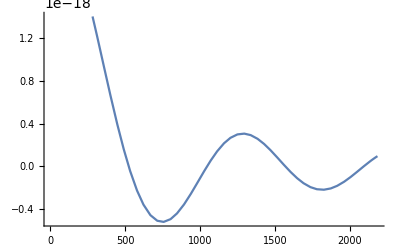

```mathematica
H[Gy2S[gy]]/.quantitiesSubs
tAtEndExpansion=(t/.(Solve[(486.59187984747547 c t)/(√(c^5/(e G sigma)))==Pi,t]/.quantitiesSubs))[[1]]
gyAtEndExpansion=S2Gy[tAtEndExpansion]
Plot[H[Gy2S[gy]]/.quantitiesSubs,{gy,1,gyAtEndExpansion*4}]
```

```mathematica
mURadiatedAsEnergy[Gy2S[200]]/.quantitiesSubs
```

1.79966×10^53

```mathematica
Plot[mURadiatedAsEnergy[Gy2S[gy]]/.quantitiesSubs,{gy,0,gyAtEndExpansion}]
```

-Graphics-

```mathematica
mU[Gy2S[gyAtEndExpansion]]/.quantitiesSubs
Plot[mU[         Gy2S[gy]]/.quantitiesSubs,{gy,0,gyAtEndExpansion}]
(* Plot[mUBook[Gy2S[gy]]/.quantitiesSubs,{gy,0,gyAtEndExpansion}] *)
```

1.85518×10^54

-Graphics-

```mathematica
Plot[mUBook[Gy2S[gy]]/.quantitiesSubs,{gy,0,gyAtEndExpansion}]
```

-Graphics-

```mathematica
mURadiatedAsEnergy[tAtEndExpansion]/mUAtStart/.quantitiesSubs
```

0.125018

```mathematica
PU[0]/.quantitiesSubs
```

2.88727×10^51

```mathematica
Plot[PU[Gy2S[gy]]/.quantitiesSubs,{gy,0,gyAtEndExpansion}]
```

-Graphics-